```mathematica
BeginPackage["BISfit`"];
```

```mathematica
BISLSfit::usage=="using least squares fit BISLSfit[data]";
```

```mathematica
Begin["MathSVM`Private`"];
```

```mathematica
LSfit[x_,y_]:=
Module[{},
F[m_,n_,r_]=∑_(k=1)^Length[x] ((x[[k]]-m)^2+(y[[k]]-n)^2-r^2)^2;NSolve[{D[F[m,n,r], m]==0&&D[F[m,n,r], n]==0&&D[F[m,n,r], r]==0},{m,n,r}]]
```

```mathematica
BISLSfit[data_]:=
Module[{X,Y,Z,i=0,sol},
X=Map[Function[x,x[[1]]Cos[-x[[2]]π/(180)]],data];
Y=Map[Function[x,x[[1]]Sin[-x[[2]]π/(180)]],data];
Z=Table[{X[[i]],Y[[i]]},{i,Length[X]}];
While[Z[[2,2]]<Z[[1,2]] &&  i<Length[Z]/3,Z=Drop[Z,1];i++];
sol=LSfit[X,Y];

i=1;
While[i<=Length[sol],
If[r<=0 /.sol[[i]],i++,
If[Im[m]>0 || Im[n]>0/.sol[[i]],i++,Break[]]]
];
{m,n,r}/.sol[[i]]
]
```

```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear will be suppressed during this calculation.

```mathematica
data=Import["D:\\study\\西安理工大学\\thesis\\论文\\标定后的数据\\calib_50.dat","Data"];
rd1=Import["D:\\study\\西安理工大学\\thesis\\论文\\标定后的数据\\calib_51.dat","Data"];

SetDirectory["D:\\study\\西安理工大学\\thesis\\论文\\nb"];
freq=Flatten[Import["freq32.dat","Data"]];
<<BISfit`
Names["BISfit`*"]
```

{BISLSfit,ColeP,Filterd,Maxd,Mind}

```mathematica
data0=data[[All,{3,4}]]

(*ColeP[data0]*)
```

{{76.54,-5.61},{75.97,-3.19},{75.17,-4.98},{74.48,-6.18},{73.81,-6.75},{73.23,-7.38},{72.52,-7.73},{72.15,-8.12},{71.68,-8.38},{71.18,-8.65},{67.1,-9.85},{63.57,-11.49},{60.78,-12.42},{58.51,-12.89},{56.64,-13.03},{55.04,-13.15},{53.64,-13.06},{52.52,-12.91},{51.52,-12.68},{49.98,-12.34},{48.76,-11.77},{47.83,-11.34},{47.,-10.84},{46.36,-10.35},{44.37,-8.63},{43.42,-7.2},{42.82,-6.39},{42.43,-5.7},{42.25,-5.25},{42.16,-4.87},{42.22,-4.78},{41.81,-4.76}}

{59.6886,-7.74105,21.1764}

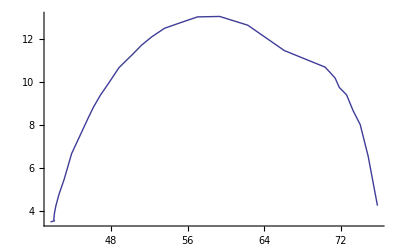

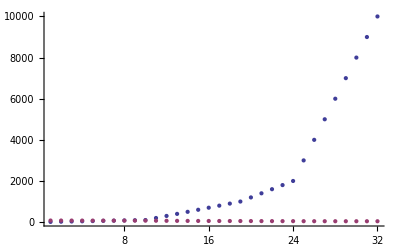

```mathematica
X=Map[ Function[x,x[[1]]Cos[-x[[2]]π/(180)]],data0];
Y=Map[ Function[x,x[[1]]Sin[-x[[2]]π/(180)]],data0];
Z=Table[{X[[i]],Y[[i]]},{i,Length[X]}];
(*filter data*)
i=0;
Z//MatrixForm;
While[Z[[2,2]]<Z[[1,2]] &&  i<Length[Z]/3,Print[Z[[1]]];Z=Drop[Z,1];i++]
```

```mathematica
l=Length[X];
F[m_,n_,r_]=∑_(k=1)^l ((X[[k]]-m)^2+(Y[[k]]-n)^2-r^2)^2;
LSF={D[F[m,n,r], m]==0&&D[F[m,n,r], n]==0&&D[F[m,n,r], r]==0};
FullSimplify[LSF];
sol=NSolve[LSF,{m,n,r}]
```

{{m→59.6886,n→-7.74105,r→-21.1764},{m→56.0583-22.0586 ⅈ,n→9.64533-1.74384 ⅈ,r→0.},{m→56.0583+22.0586 ⅈ,n→9.64533+1.74384 ⅈ,r→0.},{m→58.3495+1.2624 ⅈ,n→9.64584-13.7737 ⅈ,r→0.},{m→58.3495-1.2624 ⅈ,n→9.64584+13.7737 ⅈ,r→0.},{m→57.8705,n→7.2441,r→0.},{m→59.6886,n→-7.74105,r→21.1764}}

```mathematica
(*i=1;
While[i≤Length[sol],
If[r≤0 /.sol[[i]],i++,
If[Im[m]>0 || Im[n]>0/.sol[[i]],i++,Break[]]]
]
sol=sol[[i]]*)
```

{m→59.6886,n→-7.74105,r→21.1764}

```mathematica
(*the analytical solution*)
RR=X;
XX=Y;

T[a_,b_]:=∑_(i=1)^Length[a] a[[i]]*b[[i]]-1/Length[a]∑_(i=1)^Length[a] a[[i]] ∑_(i=1)^Length[b] b[[i]];
m=(T[RR,RR*RR+XX*XX]T[XX,XX]-T[XX,RR*RR+XX*XX]T[RR,XX])/(2(T[RR,RR]T[XX,XX]-(T[RR,XX])^2))
n=(T[XX,RR*RR+XX*XX]T[RR,RR]-T[RR,RR*RR+XX*XX]T[RR,XX])/(2(T[RR,RR]T[XX,XX]-(T[RR,XX])^2))
r=√(1/Length[RR]∑_(i=1)^Length[RR] ((RR[[i]]-m)^2+(XX[[i]]-n)^2))
r0=m+√(r^2-n^2)
r1=m-√(r^2-n^2)
a=2/π ArcCos[-n/r]
f=freq;

fc=1/32 ∑_(i=1)^32 f[[i]](r0/r1*(2r XX[[i]])/((RR[[i]]-r0)^2+XX[[i]]^2))^(1/a)
fc2=-Re[1/32 ∑_(i=1)^32 f[[i]]Re[ⅈ((XX[[i]]ⅈ+RR[[i]]-r1)/(r0-XX[[i]]ⅈ-RR[[i]]))^(1/a)]]
fc3=-Re[ ∑_(i=32)^32 f[[i]]ⅈ((XX[[i]]ⅈ+RR[[i]]-r1)/(r0-XX[[i]]ⅈ-RR[[i]]))^(1/a)]
(*b=(r0+r1)Cos[
fc3=*)
```

59.6886

-7.74105

21.1764

79.3994

39.9778

0.761761

86142.9

35093.4

49829.2

```mathematica
End[];
```

```mathematica
EndPackage[];
```